```mathematica
Clear[h,Delta]
```

### Code and Definitions

Run this code first. Then, you may jump to any subsection.

#### Spin Operators

```mathematica
Id = {{1, 0}, {0, 1}};
Sx= (1/2){{0, 1},{1, 0}};
Sy =(1/2){{0, -I},{I, 0}};
Sz = (1/2){{1, 0},{0, -1}};
```

```mathematica
{MatrixForm[Sx], MatrixForm[Sy], MatrixForm[Sz]}
```

{(0 | 1/2
1/2 | 0),(0 | -ⅈ/2
ⅈ/2 | 0),(1/2 | 0
0 | -1/2)}

#### Local spin exchange Hamiltonian

Isotropic spin-exchange Hamiltonian for adjacent sites on a ring.

```mathematica
h[Delta_] := KroneckerProduct[Sx, Sx]+KroneckerProduct[Sy, Sy]+(Delta)*(KroneckerProduct[Sz, Sz] -1/4KroneckerProduct[Id, Id]);
```

```mathematica
MatrixForm[h[1] ]
```

(0 | 0 | 0 | 0
0 | -1/2 | 1/2 | 0
0 | 1/2 | -1/2 | 0
0 | 0 | 0 | 0)

#### Probability of finding an up-spin at site x

The following function gives a list of all basis vectors that include an up-spin at site x for a chain of length L. The k-th entry equals 1 if the k-th (configuration) basis vector has an up-spin at state x. Otherwise, the entry is equal to 0. See the next section for an interpretation of the basis vectors as configuration states.

```mathematica
vec[x_, L_]:= Table[If[EvenQ[Floor[k/2^(L-x)]], 1, 0], {k, 0, 2^L-1}]
```

```mathematica
vec[1,5]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The following function gives the one-point function for the k-th eigenvector. The result is a list of length L so that each entry is {k, p(k)} with k=site and p(k)=probability of measuring an up-spin at site k. 
WARNING: E

```mathematica
Map[Function[x, Abs[x]^2], {1, 2, 3}]
```

{1,4,9}

```mathematica
t[k_,H_,keepIndices_,L_]:= Module[{Evec, norm, table, j},
Evec = Eigenvectors[H][[k]]//N;
norm = Norm[Evec]^2;
Evec= Map[Function[x, Abs[x]^2], Evec];
table =Table[{j, N[Dot[Evec, vec[j, L][[keepIndices]]]/norm]}, {j, 1, L}];
Return[table]
]
```

We rewrite the above function to have the evs=list of eigenvectors as an input so that we don’t have to compute this each time we want to compute the one-point function.

```mathematica
tp[k_, evs_,M_,L_,keepIndices_]:= Module[{Evec, norm, table, j},
Evec = evs[[k]]//N;
norm = Norm[Evec]^2;
Evec= Map[Function[x, Abs[x]^2], Evec];
table =Table[{j, N[Dot[Evec, vec[j, M][[keepIndices]]]/norm]}, {j, 1, M}];
Return[table]
]
```

#### Configurations

We translate between configuration basis and tensor basis, e.g.
{|↑↑⟩,|↑↓⟩, |↓↑⟩, |↓↓⟩} ->{(1
0) ⊗(1
0) , (1
0) ⊗(0
1), (0
1) ⊗(1
0) , (0
1) ⊗(0
1)} ->{(1
0
0
0) , (0
1
0
0)  , (0
0
1
0)   , (0
0
0
1) } 
Let L be the length of the line segment. Denote the basis vectors on the right by e_k, k =1, ..., 2^L, of length/dimension 2^L so that all the entries are zero except for the k-th entry which is 1. The example above is for L=2. We can translate to the configuration basis on the left, i.e. the basis determined by the location of the up-arrows, by writing 2^L-k in base 2. See example below for L=5. The 1-digits represent up-arrows and the 0-digits represent down-arrow. Note that you should think of each number to be made up of L {0,1}-digits by padding 0’s to the left if necessary.

```mathematica
L=5;
Table[BaseForm[2^L-k, 2], {k ,1, 2^L}]
```

{11111_2,11110_2,11101_2,11100_2,11011_2,11010_2,11001_2,11000_2,10111_2,10110_2,10101_2,10100_2,10011_2,10010_2,10001_2,10000_2,1111_2,1110_2,1101_2,1100_2,1011_2,1010_2,1001_2,1000_2,111_2,110_2,101_2,100_2,11_2,10_2,1_2,0_2}

### Hamiltonian for a ring

#### Hamiltonian for the ring of length L and fixed number of down spins

Here we trim the Hamiltonian for the ring only to consider states which contain the specified number of down spins.
For example, with a ring of length L=3, we can consider states which have exactly two down spins. We also return the kept indices which keep track of the rows and columns of the original hamiltonian we kept. These will then be used to modify the output of the vec function so that we can properly compute the one-point probabilities.

```mathematica
HringNdownspins[L_,NumDownspins_,Delta_] := Module[{hRing, H,basis,keepIndices,trimmedH, removeIndices},
hRing = KroneckerProduct[Sx, IdentityMatrix[2^(L-2)], Sx] + KroneckerProduct[Sy, IdentityMatrix[2^(L-2)], Sy]+Delta*(KroneckerProduct[Sz, IdentityMatrix[2^(L-2)], Sz]-(1/4) IdentityMatrix[2^L]);
H = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h[Delta], IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}] + hRing;
basis = Table[IntegerDigits[2^L-k, 2,L], {k ,1, 2^L}];
keepIndices = Flatten[Position[basis,x_/;Count[x,0]==NumDownspins]];
(*Sanity check if you want to make sure you're keeping the right indices:
For a single layer, L=3, N=2, indices should be 4, 6, and 7 
Print[keepIndices]; *)
trimmedH = H[[keepIndices,keepIndices]];
{trimmedH, keepIndices}
]
```

```mathematica
{H3L2N, keepIndices} = HringNdownspins[3,2,1];
MatrixForm[H3L2N]
keepIndices
```

(-1 | 1/2 | 1/2
1/2 | -1 | 1/2
1/2 | 1/2 | -1)

{4,6,7}

```mathematica
HringNdownspins[3,2,1]
```

{{{-1,1/2,1/2},{1/2,-1,1/2},{1/2,1/2,-1}},{4,6,7}}

### L=7, N=3 Eigenvalues

```mathematica
VaryingDeltaEigenvalsPlot[L_,N_]:=Module[{EigenvalsDelta},
EigenvalsDelta=Table[Eigenvalues[HringNdownspins[L,N,delta][[1]]],{delta,0,1,0.01}];
ListPlot[Table[EigenvalsDelta[[All,k]],{k,1,Length[EigenvalsDelta[[1]]]}],AxesLabel->{"Delta*100","Eigenvalues"},PlotLabel->"L="<>ToString[L]<>", "<>"N="<>ToString[N],Joined->True]]
```

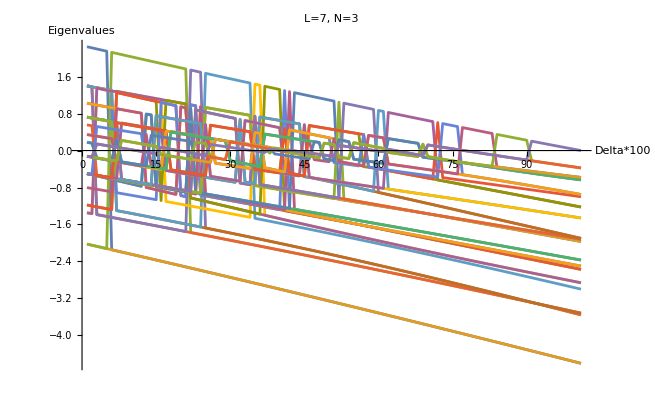

```mathematica
VaryingDeltaEigenvalsPlot[7,3]
```

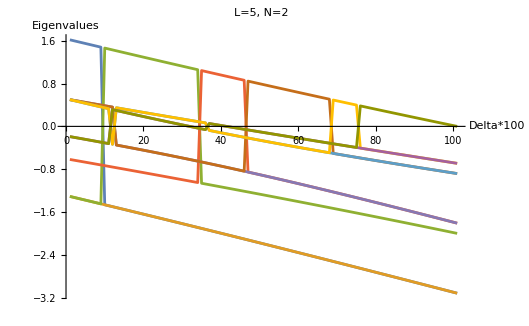

```mathematica
VaryingDeltaEigenvalsPlot[5,2]
```

```mathematica
VaryingDeltaEigenvalsPlot[9,4]
```

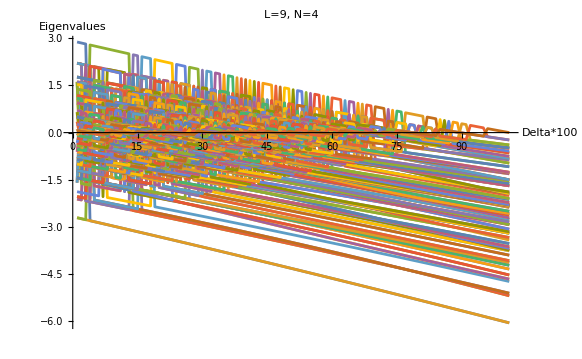

-Graphics-

$Aborted

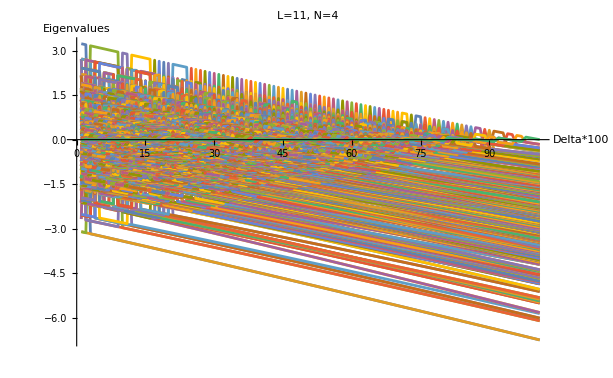

```mathematica
VaryingDeltaEigenvalsPlot[11,4]
```

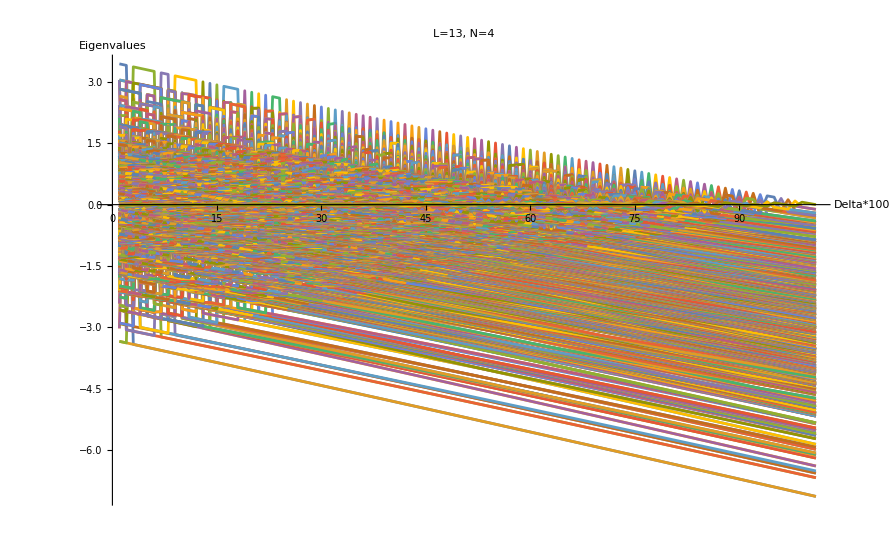

```mathematica
VaryingDeltaEigenvalsPlot[13,4]
```

```mathematica
DeltaValues=Table[delta,{delta,0,1,0.01}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
Length[L7N3EigenvalsDelta]
```

101

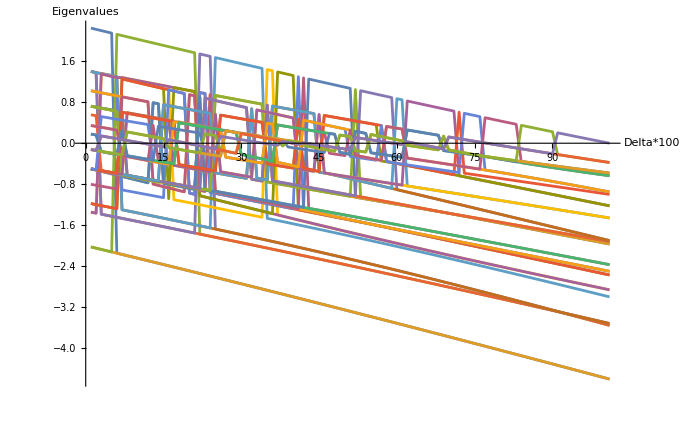

```mathematica
ListPlot[Table[L7N3EigenvalsDelta[[All,k]],{k,1,Length[L7N3EigenvalsDelta[[1]]]}],AxesLabel->{"Delta*100","Eigenvalues"},Joined->True]
```

### L=13, N=4 Eigenvalues

```mathematica
EigenvalsDelta=Table[Eigenvalues[HringNdownspins[13,4,delta][[1]]],{delta,0,1,0.01}];
```

```mathematica
DeltaValues=Table[delta,{delta,0,1,0.01}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
EigenvalsDelta[[All,1]]
```

{3.43891,3.40213,-3.41262,-3.44948,-3.48638,-3.5233,-3.56025,-3.59723,-3.63424,-3.67128,-3.70834,-3.74544,-3.78255,-3.8197,-3.85687,-3.89407,-3.9313,-3.96855,-4.00582,-4.04312,-4.08044,-4.11779,-4.15517,-4.19256,-4.22998,-4.26743,-4.30489,-4.34238,-4.3799,-4.41743,-4.45499,-4.49257,-4.53017,-4.56779,-4.60543,-4.64309,-4.68078,-4.71848,-4.7562,-4.79395,-4.83171,-4.8695,-4.9073,-4.94512,-4.98296,-5.02082,-5.0587,-5.09659,-5.13451,-5.17244,-5.21039,-5.24836,-5.28634,-5.32434,-5.36236,-5.4004,-5.43845,-5.47651,-5.5146,-5.5527,-5.59081,-5.62895,-5.66709,-5.70526,-5.74343,-5.78163,-5.81983,-5.85805,-5.89629,-5.93454,-5.97281,-6.01109,-6.04938,-6.08769,-6.12601,-6.16434,-6.20269,-6.24105,-6.27942,-6.31781,-6.35621,-6.39462,-6.43304,-6.47148,-6.50993,-6.54839,-6.58686,-6.62535,-6.66384,-6.70235,-6.74087,-6.7794,-6.81794,-6.8565,-6.89506,-6.93364,-6.97222,-7.01082,-7.04943,-7.08805,-7.12668}

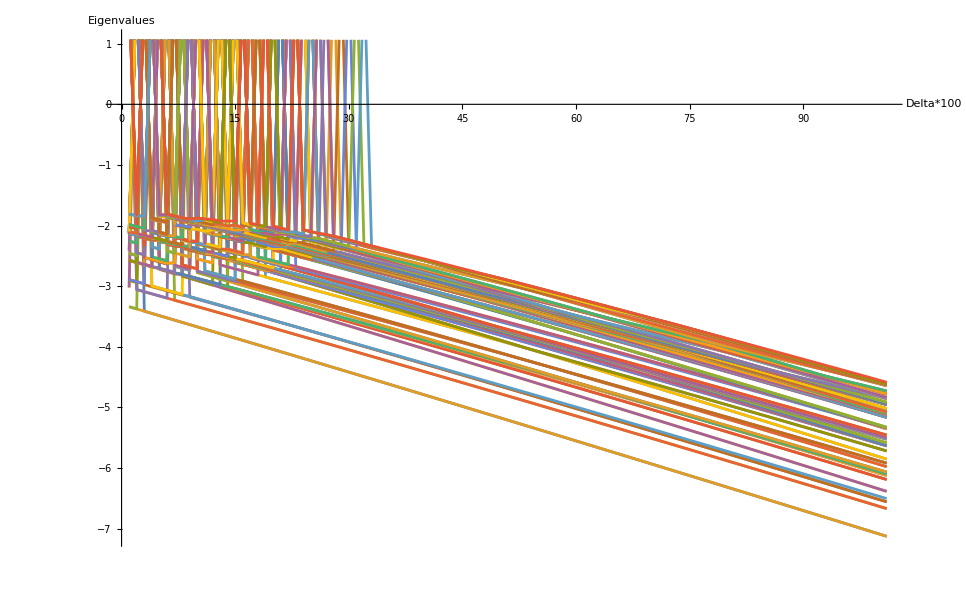

```mathematica
ListPlot[Table[EigenvalsDelta[[All,k]],{k,1,Length@DeltaValues}],Joined->True,AxesLabel->{"Delta*100","Eigenvalues"}]
```

-3.33898

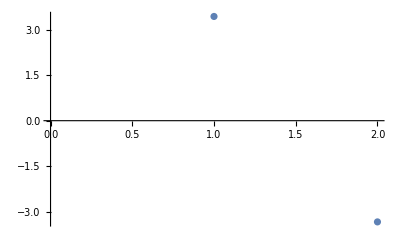

```mathematica
EigenvalsDelta[[1]][[2]]
ListPlot[{EigenvalsDelta[[1]][[1]],EigenvalsDelta[[1]][[2]]}]
```